## 4강 대수학

전경원 <ruddyscent@gmail.com>

2014년 9월 26일 금요일

## 다항식의 인수분해와 전개

다항식의 인수분해: 근

다항식의 전개: y축의 교점, 큰 수의 경향

```mathematica
Factor[-1+3x+x^2]
```

-1+3 x+x^2

#### 실습

f(x)=1+5x+2 x^3+10 x^4일 때,

Plot을 이용하여 f(x)의 실수 해를 추정해보자.

Factor를 이용하여 f(x)의 실수 해를 찾아보자.

## Solve와 NSolve로 다항식의 근 찾기

Solve와 N을 이용하여 다항식 x^3-15x+2의 근을 추정해보자.

위의 다항식의 해를 NSolve를 이용하여 구해보자.

## Reduce로 방정식과 부등식의 근 찾기

함수 f(x)=(x^3+5 x^2+4x+5)/(√(x^2+2x-3))의 정의역은 어떻게 될까?

양의 x가 증가할 때, 함수 f(x)를 분석해보자.

## 복소수 결괏값의 이해

매스매티카가는 -8의 삼중근 값으로 복소수를 반환한다.

```mathematica
(-8)^(1/3)//N
```

1.+1.73205 ⅈ

실수 계산의 결과로 복소수를 얻게 되는 경우가 종종있다.

```mathematica
Log[-2]
```

ⅈ π+Log[2]

```mathematica
ArcSin[2.]
```

1.5708-1.31696 ⅈ

```mathematica
Solve[x^2==-4,x]
```

{{x→-2 ⅈ},{x→2 ⅈ}}

```mathematica
Reduce[1+x+3 x^2+x^3==0,x,Cubics->True]
```

x==-1-(9-√57)^(1/3)/3^(2/3)-2/(3 (9-√57))^(1/3)||x==-1+((1+ⅈ √3) (9-√57)^(1/3))/(2 3^(2/3))+(1-ⅈ √3)/(3 (9-√57))^(1/3)||x==-1+((1-ⅈ √3) (9-√57)^(1/3))/(2 3^(2/3))+(1+ⅈ √3)/(3 (9-√57))^(1/3)

Reduce의 세 번째 매개변수로 Reals을 넣으면 실수해만 반환한다.

```mathematica
Reduce[ⅇ^x==-2,x,Reals]
```

False

```mathematica
Reduce[Sin[x]==2,x,Reals]
```

False

```mathematica
Reduce[x^2==-4,x,Reals]
```

False

```mathematica
Reduce[x^3==-8,x,Reals]
```

x==-2

```mathematica
Reduce[1+x+3 x^2+x^3==0,x,Reals,Cubics->True]
```

x==-1-(9-√57)^(1/3)/3^(2/3)-2/(3 (9-√57))^(1/3)

```mathematica
Reduce[x^3-15x+2==0,x,Reals,Cubics->True]//ToRadicals
%//ComplexExpand//Simplify
```

x==-(5 (1+ⅈ √3))/(2 (-1+2 ⅈ √31)^(1/3))-1/2 (1-ⅈ √3) (-1+2 ⅈ √31)^(1/3)||x==-(5 (1-ⅈ √3))/(2 (-1+2 ⅈ √31)^(1/3))-1/2 (1+ⅈ √3) (-1+2 ⅈ √31)^(1/3)||x==5/(-1+2 ⅈ √31)^(1/3)+(-1+2 ⅈ √31)^(1/3)

x==-2 √5 Cos[1/3 ArcTan[2 √31]]||x+√15 Sin[1/3 ArcTan[2 √31]]==√5 Cos[1/3 ArcTan[2 √31]]||x==√5 (Cos[1/3 ArcTan[2 √31]]+√3 Sin[1/3 ArcTan[2 √31]])

### 유리수 제곱근을 복소수로 정한 이유는?

매스매티카가 찾은 -8의 세제곱근은

```mathematica
ComplexExpand[(-8)^(1/3)]
```

1+ⅈ √3

사실, -8의 세제곱근은 하나가 아니다.

```mathematica
Reduce[x^3==-8,x]
```

x==-2||x==1-ⅈ √3||x==1+ⅈ √3

먼저, 제곱승을 하는 함수는 Power라는 것을 인지하자.

```mathematica
x^p//FullForm
```

Power[x,p]

음수에 양의 유리수 거듭제곱을 할 때, 지수의 분모가 홀수이면 실수를 반환하는 함수를 지수 함수를 생각해보자. 이 함수는 분자가 짝수이면 양, 홀수이면 음이 된다.

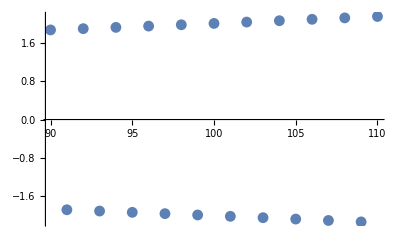

```mathematica
realPower[x_,p_]:=
If[x<0&&Element[p,Rationals],
If[OddQ[Denominator[p]],
If[OddQ[Numerator[p]],
-Power[-x,p],Power[-x,p]
],Power[x,p]
],Power[x,p]
]
Table[{x,realPower[-2,x/99]},{x,90,110}
]//ListPlot
realPower=.
```

이와는 달리 -8의 세제곱근 중, 제일 작은 편각을 갖는 주세제곱근을 -8의 세제곱근으로 정해보자.

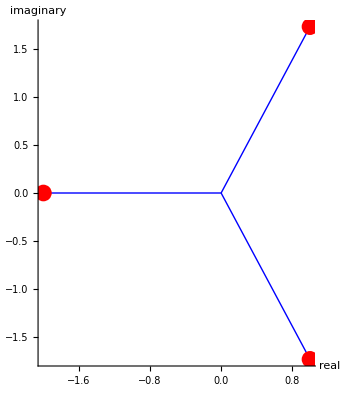

```mathematica
NSolve[x^3==-8,x];
Graphics[
{{Thick,Blue,Line[{{0,0},{Re[x],Im[x]}}]/.%},{Red,PointSize[.03],Point[{Re[x],Im[x]}]/.%}},
Axes->True,AxesLabel->{"real","imaginary"}
]
```

주제곱근을 사용하면 지수함수가 연속성을 갖게 된다.

```mathematica
N[{(-2)^(311/99),(-2)^(312/99)}]//Column
```

-7.96732-3.79246 ⅈ
-7.89809-4.07175 ⅈ

지수함수가 연속이 되면, 지수에 오는 유리수에 극한을 취해서 무리수 제곱값도 찾을 수 있다.

```mathematica
N[{(-2)^(311/99),(-2)^π,(-2)^(312/99)}]//Column
```

-7.96732-3.79246 ⅈ
-7.96618-3.7974 ⅈ
-7.89809-4.07175 ⅈ

복소수 함수의 연속성을 그래프로 확인해보자.

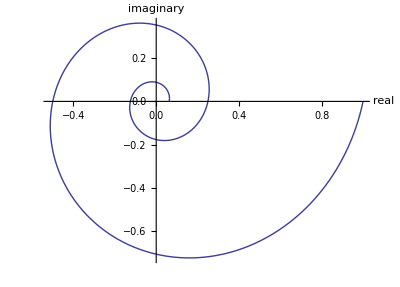

```mathematica
z=Table[(-2)^x,{x,-4,0,.01}];
ListLinePlot[Transpose@{Re[z],Im[z]},
AspectRatio->Automatic,Axes->True,AxesLabel->{"real","imaginary"}]
Clear[z];
```

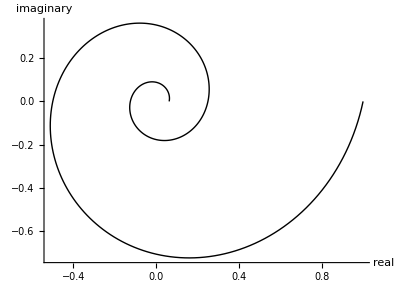

```mathematica
pwrs=Table[(-2)^x,{x,-4,0,.01}];
Graphics[Line[Table[{Re[z],Im[z]},{z,pwrs}]],Axes->True,AxesLabel->{"real","imaginary"}]
Clear[pwrs];
```

## 유리함수

### 방정식의 풀이

```mathematica
Solve[((x+3)(x-1))/(x-1)==0,x]
```

### 분수 식의 정리

```mathematica
Simplify[(1-x^5)/(1-x)]
```

```mathematica
Expand[(1-x)(1+x+x^2+x^3+x^4)]
```

팔레트를 이용하여 부분적으로 정리할 수도 있다.

```mathematica
(x^4+5 x^3+8 x^2+7x+3)/(3 x^4+14 x^3+18 x^2+10x+3)
```

### TraditionalForm의 이용

```mathematica
x-3
```

```mathematica
x-3//TraditionalForm
```

### 수직 점근선

분모의 해 중에서 분자의 해가 아닌 것은 그래프에서 수직 점근선으로 나타낸다.

```mathematica
k[x_]:=(x^4+3 x^3-x^2+5x-4)/(x^2-9)
```

```mathematica
Plot[k[x],{x,-10,10},Exclusions->{x^2-9==0},ExclusionsStyle->Directive[Gray,Dashed]]
```

### 다항식의 나눗셈

```mathematica
k[x_]:=(x^4+3 x^3-x^2+5x-4)/(x^2-9)
```

```mathematica
num=Numerator[k[x]]
```

```mathematica
den=Denominator[k[x]]
```

```mathematica
Expand[(8+3x+x^2)(x^2-9)+(68+32x)]==x^4+3 x^3-x^2+5x-4
```

```mathematica
Plot[{k[x],q[x]},{x,-15,15},Exclusions->{x^2-9==0},ExclusionsStyle->Directive[Gray,Dashed]]
```

### 부분분수분해

```mathematica
Apart[(x^4+3 x^3-x^2+5x-4)/(x^2-9)]
```

```mathematica
Together[8+82/(3 (-3+x))+3 x+x^2+14/(3 (3+x))]
```

## 더욱 많은 표현

```mathematica
Simplify[Log[ⅇ^x]]
```

Log[ⅇ^x]

```mathematica
Simplify[Log[ⅇ^x],x∈Reals]
```

x

```mathematica
Simplify[√(x^2)]
```

√(x^2)

```mathematica
Simplify[√(x^2),x>0]
```

x

```mathematica
Simplify[√(x^2),x<0]
```

-x

#### 해의 검증

```mathematica
Clear[f,x];
f[x_]:=x^3-2x+9
```

```mathematica
Solve[f[x]==0,x]
realRoot=x/.%[[1]]
```

```mathematica
f[realRoot]
Simplify[%]
```

### 삼각함수

다음 삼각방정식을 증명해보자.
(sin(a t)+sin((2-a)t))/(2sin(t))=cos((1-a)t)

## 일반 방정식의 풀이

```mathematica
Plot[{1-x^2,Sin[x]},{x,-4,4}]
```

## 차분 방정식의 풀이

2014 람보르기니 우라칸 쿠페는 3억7,100만원입니다. 지금 돈이 한 푼도 없으므로, 연 8.9%의 이자로 5년 상환 대출을 받아 차를 사려고 합니다. 매달 정액 상환한다면 월 납입금은 얼마나 될까요?